```mathematica
DrawWithWithoutAndContract2[g_]:=Block[{edges,full,implied={},mpg},
edges=EdgeList[GraphComplement[g]];
mpg=CollectMPGEdges[g];
Monitor[
Table[With[{
without=Graph[g,VertexLabels->"Name",GraphHighlight->{e[[1]],e[[2]]},GraphHighlightStyle->"Thick",GraphLayout->"TutteEmbedding", ImageSize->40],
contract =Graph[VertexContract[g,{e[[1]],e[[2]]}],VertexLabels->"Name",GraphHighlight->{e[[1]]},GraphHighlightStyle->"Thick",GraphLayout->"TutteEmbedding", ImageSize->40],
with=Graph[EdgeAdd[g,e],GraphHighlight->e,GraphLayout->"TutteEmbedding", VertexLabels->"Name",GraphHighlightStyle->"Thick", ImageSize->40]
},
With[
{ffull=FindFullFormula[with],
fwithout=FindFullFormula[without],
fcontract=Map[SymbolReplace[#,e]&,FindFullFormula[contract]]
},
implied=Join[implied,ImpliedNodes[fcontract,ffull]];
Labeled[
Graph[
JoinGraphs[
FormulaGraphReverse2[ffull],
FormulaGraphReverse2[fwithout],
FormulaGraphReverse2[fcontract]
], ImageSize->600
],
If[MemberQ[mpg,e],Style[e,Red],e]]
]
],{e,Sort[Map[SortEdge,edges]]}],
e]
]
```

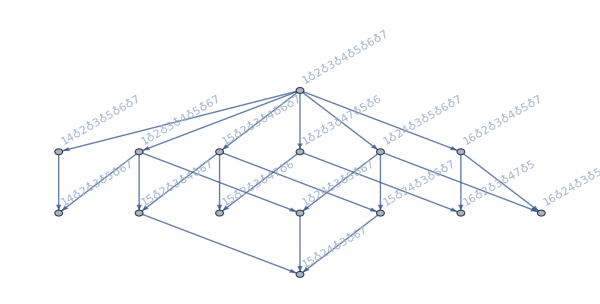
{-Graphics-1<->4,-Graphics-1<->5,-Graphics-1<->6,-Graphics-2<->4,-Graphics-4<->7,-Graphics-6<->7}

```mathematica
DrawWithWithoutAndContract2[ReadGrof[5]]
```